# Analise dos pontos do “Caso A”

Os pontos do Caso A são da forma

        z = ((x,1/3,1-x-1/3), (1-x-1/3,1/3,x)) = (B, B’)
Utilizamos a parameterisação
       B: (x,1/3,1-x-1/3) = A + t v⃗,      t ∈  [0,1]
       B’: (1-x-1/3,1/3,x) = A + t v⃗,      t ∈  [-1,0]
 onde A(1/3,1/3,1/3) e v⃗ é o vetor diretor v⃗= (1/3,1/3,1/3). Assim, podemos reescrever B(x_1, x_2, x_3) parametricamente em função de t como
         x_1 = 1/3 - t 1/3
         x_2=1/3
         x_3=1/3+t 1/3
Lembramos que o campo F é dado por F=(F_1^x, F_2^x, F_3^x, F_1^y, F_2^y, F_3^y), sendo por exeplo,
     F_1^x(z) = -x_1+ 1/3(e^(-α y_1)/(e^(-α y_1)+ e^(-α y_2))+e^(-α y_1)/(e^(-α y_1)+ e^(-α y_3)))
e
     F_1^y(z) = -y_1+ 1/3(e^(-α x_1)/(e^(-α x_1)+ e^(-α x_2))+e^(-α x_1)/(e^(-α x_1)+ e^(-α x_3))),
sendo z = ((x_1, x_2, x_3), (y_(1,)y_2, y_3)); ou seja x_1=x=1/3-t 1/3, etc.

## Existência

Se z é um equilíbrio, então F(z)=0, logo, F_3^x(z)= 0; isto é,
x_3= 1/3 e^-αy_3/(e^-αy_3+e^-αy_1) + 1/3 e^-αy_3/(e^-αy_3+e^-αy_2)
ou seja,
1/3-t 1/3= 1/3(e^(-α (1/3+1/3 t))/(e^(-α (1/3+1/3 t))+ e^(-α (1/3-1/3 t)))+e^(-α (1/3+1/3 t))/(e^(-α (1/3+1/3 t))+ e^(-α 1/3)))

```mathematica
Exp[-α (1/3+1/3 t)]/(Exp[-α (1/3+1/3 t)]+Exp[-α (1/3-1/3 t)])+Exp[-α (1/3+1/3 t)]/(Exp[-α (1/3+1/3 t)]+Exp[-α 1/3])//FullSimplify
```

1/(1+ⅇ^((t α)/3))+1/(1+ⅇ^((2 t α)/3))

```mathematica
g[α_, t_]=1/(1+ⅇ^((t α)/3))+1/(1+ⅇ^((2 t α)/3));
```

```mathematica
Manipulate[Plot[{1-t,g[α,t]},{t,-1,1},PlotRange->{{-1,1},{0,2}},AspectRatio->1],{{α,7},0,20},Paneled->False]
```

Derivada da curva laranja em t=0

```mathematica
D[g[α,t],t]/.{t-> 0}
```

-α/4

ou seja o equilíbrio do Caso A só existe quando α > 4. É relativamente simples mostrar que é único quando t ∈ [0,1], pois g(α, t) é monotona decrescente se t ∈ [0,1]. (Da mesma maneira mostramos que existe um único equilíbrio deste tipo para t ∈ [-1,0]; ou seja utilizando a monotonicidade de da função g)

```mathematica
D[g[α,t],{t,2}]//FullSimplify
```

1/36 α^2 (Sech[(t α)/6]^2 Tanh[(t α)/6]+4 Sech[(t α)/3]^2 Tanh[(t α)/3])

```mathematica
Manipulate[Plot[1/36 α^2 (Sech[(t α)/6]^2 Tanh[(t α)/6]+4 Sech[(t α)/3]^2 Tanh[(t α)/3]),{t,0,1},PlotRange->{{0,1},{-0.1,1}}],{α,0,20}];
```

Uma outra forma de ver a dependencia de α; (isto é de fato o mesmo grafico anterior porém sem Manipula)

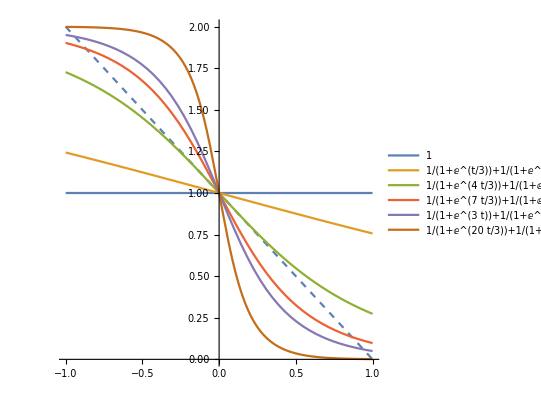

```mathematica
p2=Plot[1-t,{t,-1,1},PlotStyle->Dashed,AspectRatio->1];
p1=Plot[Evaluate@Table[g[α,t],{α,{0,1,4,7,9,20}}],{t,-1,1},AspectRatio->1,PlotLegends->"Expressions"];
Show[p2,p1]
```

## Estabilidade

Determinamos o Jacobiano de F em um ponto z ∈ 𝔜 qualquer, isto é em z=((x_1, x_2, x_3), (y_(1,)y_2, y_3)).

```mathematica
JF={
{-1,0,0,1/3 ((ⅇ^(-2 y1 α) α)/((ⅇ^(-y1 α)+ⅇ^(-y2 α))^2)-(ⅇ^(-y1 α) α)/(ⅇ^(-y1 α)+ⅇ^(-y2 α))+(ⅇ^(-2 y1 α) α)/((ⅇ^(-y1 α)+ⅇ^(-y3 α))^2)-(ⅇ^(-y1 α) α)/(ⅇ^(-y1 α)+ⅇ^(-y3 α))),(ⅇ^(-y1 α-y2 α) α)/(3 (ⅇ^(-y1 α)+ⅇ^(-y2 α))^2),(ⅇ^(-y1 α-y3 α) α)/(3 (ⅇ^(-y1 α)+ⅇ^(-y3 α))^2)}, 
{0,-1,0,(ⅇ^(-y1 α-y2 α) α)/(3 (ⅇ^(-y1 α)+ⅇ^(-y2 α))^2),1/3 ((ⅇ^(-2 y2 α) α)/((ⅇ^(-y1 α)+ⅇ^(-y2 α))^2)-(ⅇ^(-y2 α) α)/(ⅇ^(-y1 α)+ⅇ^(-y2 α))+(ⅇ^(-2 y2 α) α)/((ⅇ^(-y2 α)+ⅇ^(-y3 α))^2)-(ⅇ^(-y2 α) α)/(ⅇ^(-y2 α)+ⅇ^(-y3 α))),(ⅇ^(-y2 α-y3 α) α)/(3 (ⅇ^(-y2 α)+ⅇ^(-y3 α))^2)},
{0,0,-1,(ⅇ^(-y1 α-y3 α) α)/(3 (ⅇ^(-y1 α)+ⅇ^(-y3 α))^2),(ⅇ^(-y2 α-y3 α) α)/(3 (ⅇ^(-y2 α)+ⅇ^(-y3 α))^2),1/3 ((ⅇ^(-2 y3 α) α)/((ⅇ^(-y1 α)+ⅇ^(-y3 α))^2)-(ⅇ^(-y3 α) α)/(ⅇ^(-y1 α)+ⅇ^(-y3 α))+(ⅇ^(-2 y3 α) α)/((ⅇ^(-y2 α)+ⅇ^(-y3 α))^2)-(ⅇ^(-y3 α) α)/(ⅇ^(-y2 α)+ⅇ^(-y3 α)))},
{1/3 ((ⅇ^(-2 x1 α) α)/((ⅇ^(-x1 α)+ⅇ^(-x2 α))^2)-(ⅇ^(-x1 α) α)/(ⅇ^(-x1 α)+ⅇ^(-x2 α))+(ⅇ^(-2 x1 α) α)/((ⅇ^(-x1 α)+ⅇ^(-x3 α))^2)-(ⅇ^(-x1 α) α)/(ⅇ^(-x1 α)+ⅇ^(-x3 α))),(ⅇ^(-x1 α-x2 α) α)/(3 (ⅇ^(-x1 α)+ⅇ^(-x2 α))^2),(ⅇ^(-x1 α-x3 α) α)/(3 (ⅇ^(-x1 α)+ⅇ^(-x3 α))^2),-1,0,0},
{(ⅇ^(-x1 α-x2 α) α)/(3 (ⅇ^(-x1 α)+ⅇ^(-x2 α))^2),1/3 ((ⅇ^(-2 x2 α) α)/((ⅇ^(-x1 α)+ⅇ^(-x2 α))^2)-(ⅇ^(-x2 α) α)/(ⅇ^(-x1 α)+ⅇ^(-x2 α))+(ⅇ^(-2 x2 α) α)/((ⅇ^(-x2 α)+ⅇ^(-x3 α))^2)-(ⅇ^(-x2 α) α)/(ⅇ^(-x2 α)+ⅇ^(-x3 α))), (ⅇ^(-x2 α-x3 α) α)/(3 (ⅇ^(-x2 α)+ⅇ^(-x3 α))^2),0,-1,0},
{(ⅇ^(-x1 α-x3 α) α)/(3 (ⅇ^(-x1 α)+ⅇ^(-x3 α))^2),(ⅇ^(-x2 α-x3 α) α)/(3 (ⅇ^(-x2 α)+ⅇ^(-x3 α))^2),1/3 ((ⅇ^(-2 x3 α) α)/((ⅇ^(-x1 α)+ⅇ^(-x3 α))^2)-(ⅇ^(-x3 α) α)/(ⅇ^(-x1 α)+ⅇ^(-x3 α))+(ⅇ^(-2 x3 α) α)/((ⅇ^(-x2 α)+ⅇ^(-x3 α))^2)-(ⅇ^(-x3 α) α)/(ⅇ^(-x2 α)+ⅇ^(-x3 α))),0,0,-1}
};
```

Avaliamos agora o Jacobiano do campo no ponto do Caso A,

```mathematica
JFequil=JF/.{x1->1/3-t 1/3,x2-> 1/3,x3->1-(1/3-t 1/3)-1/3,y1-> 1-(1/3-t 1/3)-1/3,y2->1/3,y3-> 1/3-t 1/3}//FullSimplify;
```

Para determinar o especto, resulta mais simples adicionar a matriz identidade a matriz acima

```mathematica
JFminusId=JFequil+IdentityMatrix[6];
```

```mathematica
Eigenvalues[JFminusId]
```

{0,0,-(α (3+2 Cosh[(t α)/3]+Cosh[(2 t α)/3]))/(6 (Cosh[(t α)/6]+Cosh[(t α)/2])^2),(α (3+2 Cosh[(t α)/3]+Cosh[(2 t α)/3]))/(6 (Cosh[(t α)/6]+Cosh[(t α)/2])^2),-1/4 α Sech[(t α)/6]^2,1/4 α Sech[(t α)/6]^2}

O ultimo auto-valor é maior a todos os outros para tudo x ∈ [0,1/3] e tudo α >0; portanto podemos focar a nossa atenção nele, ou seja (observamos que subtraimos 1 por ter adicionado 1 na diagonal da matriz original)

```mathematica
λ[α_, t_]=1/4 α Sech[(t  α)/6]^2-1;
```

```mathematica
Solve[λ[α,t]==0,t,Reals]
```

{{t→ConditionalExpression[-(6 ArcCosh[(√α)/2])/α,α>4]},{t→ConditionalExpression[(6 ArcCosh[(√α)/2])/α,α>4]}}

```mathematica
Manipulate[Plot[λ[α,t],{t,0,1},
PlotRange->{{0,1},{-1,2}},
ImageSize->300,
AspectRatio->1,
GridLines-> {{(6 ArcCosh[(√α)/2])/α,{t/.FindRoot[-(1-t)+g[α, t],{t,0.7}],Directive[Red,Dashed]}},None}],
{α,4.001,20}]
```

FindRoot::nlnum: The function value {-0.3+g[7.18,0.7]} is not a list of numbers with dimensions {1} at {t} = {0.7}.

ReplaceAll::reps: {FindRoot[-(1-t)+g[FE`α$$71,t],{t,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.3+g[7.18,0.7]} is not a list of numbers with dimensions {1} at {t} = {0.7}.

ReplaceAll::reps: {FindRoot[-(1-t)+g[FE`α$$71,t],{t,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.3+g[7.18,0.7]} is not a list of numbers with dimensions {1} at {t} = {0.7}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[-(1-t)+g[FE`α$$71,t],{t,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Na figura acima, a linha vertical cinza mostra o lugar exato onde o auto-valor λ (maior em tudo t ∈ [0,1] aos outros auto-valores) corta o eixo x; a linha pontilhada vermelha mostra o valor de t que satisfaz a condição de equilíbrio. Concluímos disto que para qualquer α > 4, o equilíbrio do Caso A é estável pois o valor de t de equilíbrio esta sempre a direita do lugar onde o auto-valor corta o eixo x -- ou seja t ocorre onde o auto-valor é negativo portanto todos os auto-valores são negativos (⇒ estabilidade).

# Analise dos pontos do “Caso B”

Para os pontos do Caso B utilizamos a parametrização
       B:  A + t v⃗,      t ∈  [0,1]
       B’:  A + t v⃗,      t ∈  [-1,0]
 onde A(1/3,1/3,1/3) e v⃗ é o vetor diretor v⃗= (-1/3,1/6,1/6). Assim, podemos reescrever B(x_1, x_2, x_3) e B'(y_1, y_2, y_3) para-metricamente em função de t como

```mathematica
{{Subscript[y, 1] =1/3 - t 1/3,, Subscript[x, 1] =1/3 + t 1/3}, {Subscript[y, 2] =1/3 + t 1/6,, Subscript[x, 2] =1/3 - t 1/6}, {Subscript[y, 3] =1/3 + t 1/6,, Subscript[x, 3] =1/3 - t 1/6}}
```

No equilíbrio temos 

          x_2=1/3 e^-αy_2/(e^-αy_2+e^-αy_1) + 1/3 e^-αy_2/(e^-αy_2+e^-αy_3)
ou seja,
         1/3-t 1/6= 1/3 1/(1+e^(tα/2)) + 1/6
que equivale a 
        α t = Log((t+1)/(1-t))

```mathematica
h[t_]=Log[(t+1)/(1-t)];
```

```mathematica
Manipulate[Plot[{α t,h[t]},{t,-1,1},PlotRange->{{-1,1},{-5,5}},AspectRatio->1],{{α,1},0,20},Paneled->False]
```

Derivada da curva laranja em t=0

```mathematica
D[h[t],t]/.{t-> 0}
```

2

Concluímos disto ultimo que os pontos que pertencem ao Caso B só podem ser equilíbrios se α > 2. O seguinte é uma outra maneira de vermos a dependência de α.

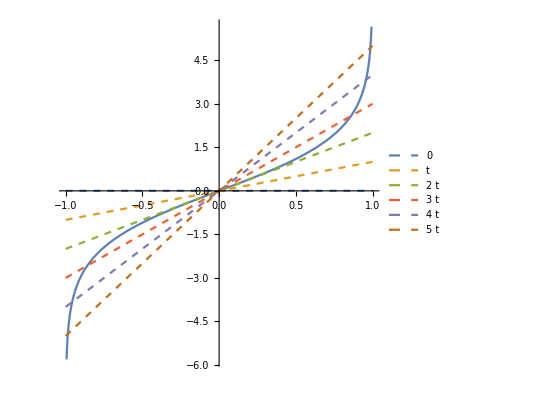

```mathematica
p2=Plot[h[t],{t,-1,1},AspectRatio->1];
p1=Plot[Evaluate@Table[α t,{α,{0,1,2,3,4,5}}],{t,-1,1},AspectRatio->1,PlotLegends->"Expressions",PlotStyle->Dashed];
Show[p2,p1]
```

A medida que α aumenta, o lugar do equilíbrio se afasta mais do centro do simplice (t → 1) e no limite α → ∞ temos t=1.

## Estabilidade

Avaliamos o Jacobiano do Campo (JF acima, na analise do Campo A, deve ser avaliado primeiro) no equilíbrio do Caso B, utilizando a parametrização  fornecida em termos de t.

```mathematica
JFequil=JF/.{x1->1/3-t 1/3,x2-> 1/3+t 1/6,x3->1/3+t 1/6,y1-> 1/3+t 1/3,y2->1/3-t 1/6,y3-> 1/3-t 1/6}//FullSimplify;
```

```mathematica
JFminusId=JFequil+IdentityMatrix[6];
```

```mathematica
Eigenvalues[JFminusId]
```

{0,0,-1/4 α Sech[(t α)/4]^2,1/4 α Sech[(t α)/4]^2,-1/12 α (2+Cosh[(t α)/2]) Sech[(t α)/4]^2,1/12 α (2+Cosh[(t α)/2]) Sech[(t α)/4]^2}

```mathematica
Manipulate[Plot[{-1/4 α Sech[(t α)/4]^2-1,1/4 α Sech[(t α)/4]^2-1,-1/12 α (2+Cosh[(t α)/2]) Sech[(t α)/4]^2-1,1/12 α (2+Cosh[(t α)/2]) Sech[(t α)/4]^2-1},{t,0,1}],{α,0,200}]
```

```mathematica
1/12 α (2+Cosh[(t α)/2]) Sech[(t α)/4]^2-1//FullSimplify
```

1/12 (2 (-6+α)+α Sech[(t α)/4]^2)

Realmente só importa o que ocorre em t=1, como a função é monotona decrescente, se em t=1 é positiva então é positiva no intervalo tudo ou seja para tudo t∈[0,1]. Fazemos portanto

```mathematica
2 (-6+α)+α Sech[(t α)/4]^2/.{t->1}
```

2 (-6+α)+α Sech[α/4]^2

```mathematica
FindRoot[-12+2α+α Sech[α/4]^2==0,{α,0.9}]
```

{α→5.35559}

O seguinte grafico mostra 2 (-6+α)+α Sech[α/4]^2 em função de α. Sabemos que a função é negativa para todo α < 5.35559 (pelo FindRoot acima); mas tal vez podemos justificar analiticamente utilizando uma cota desta função. O grafico também mostra várias outras cotas, mas também analiticamente dificeis de mostrar o lugar exato onde estas cortam o eixo x.

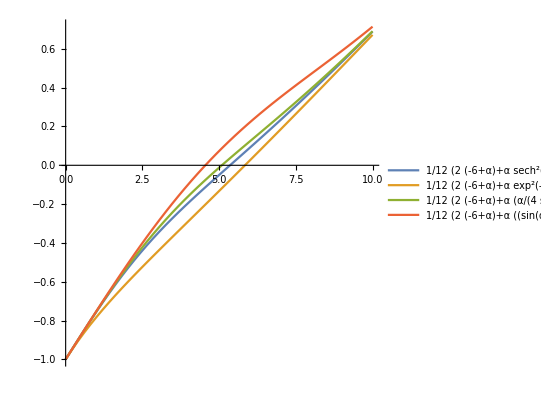

```mathematica
Plot[{1/12(2(-6+α)+α Sech[α/4]^2),1/12(2(-6+α)+α Exp[-α/4]^2),1/12(2(-6+α)+α ((α/4)/Sinh[α/4])^4), 1/12(2(-6+α)+α (Sin[α/4]/(α/4))^2)},{α,0,10},AspectRatio->1,PlotLegends->"Expressions"]
```